```mathematica
<<Local`SrednickiInit`
```

11.1) a) Consider a theory of a two real scalar ﬁelds A and B with an interaction L1 = gAB2. Assuming that mA > 2mB , compute the total decay rate of the A particle at tree level. 
b) Consider a theory of a real scalar ﬁeld ϕ and a complex scalar ﬁeld χ with L1 = gϕχ† χ. Assuming that mϕ > 2mχ , compute the total decay rate of the ϕ particle at tree level.

We take the definitions of Chapter 10 and the tree diagram as in Problem 10.3

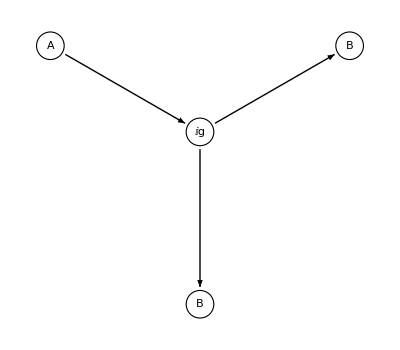

```mathematica
GraphPlot[{1->6,6->2,6->3},EdgeRenderingFunction->(Switch[Last[#2],
6,{Black, Arrow[#1,.1]},
2,{Black, Arrow[#1,.1]},
3,{Black,Arrow[#1,.1]},
_,{Black,Arrow[#1,.1],Line[#1],Black,Inset[Text[Last[#2]],Mean[#1],Background->White]}]&),
VertexRenderingFunction->(
Switch[#2,
1,{White,EdgeForm[Black],Disk[#,.08],Black,Text["A",#1]},
2,{White,EdgeForm[Black],Disk[#,.08],Black,Text["B",#1]},
3,{White,EdgeForm[Black],Disk[#,.08],Black,Text["B",#1]},
6,{White,EdgeForm[Black],Disk[#,.08],Black,Text["ⅈg",#1]}]
&)
]
```

```mathematica
DefPrint["e1148",dΓ->1/(2 k[1,0])Abs[𝒯]^2 dLIPS[k[1]]]
```

e1148: dΓ→(Abs[𝒯]^2 dLIPS[k_1^1])/(2 k_10^10)

```mathematica
DefPrint["e1130",dLIPS[k[1]]->Abs[k[space@2]]/(16 π^2 √s)Subscript[dΩ, CM]]
```

e1130: dLIPS[k_1^1]→(Abs[k_2^2] dΩ_CM)/(16 π^2 √s)

```mathematica
DefPrint["e1014",⟨f|i⟩->(2 π)^4 DiracDelta[k[in]-k[out]]ⅈ𝒯]
```

e1014: ⟨f|i⟩→16 π^4 ⅈ𝒯 DiracDelta[k_in^in-k_out^out]

```mathematica
subT=𝒯->ⅈg
e1148/.subT/.e1130
dDecay=%/.s->(Subscript[m, 1])^2/.k[1,0]->Subscript[m, 1]
```

𝒯→ⅈg

dΓ→(Abs[ⅈg]^2 Abs[k_2^2] dΩ_CM)/(32 π^2 √s k_10^10)

dΓ→(Abs[ⅈg]^2 Abs[k_2^2] dΩ_CM)/(32 π^2 m_1 √(m_1^2))

```mathematica
{k[space@2]^2+Subscript[m, 2]^2==Subscript[e, 2]^2,
Subscript[e, 1]==2 Subscript[e, 2]}
Eliminate[%,Subscript[e, 2]]
Solve[%,k[space@2]][[2,1]]
subm=%/.Subscript[e, 1]->Subscript[m, 1](*center of mass*)
sub=dDecay/.subm
Γ->IntegralOp[{Subscript[Ω, CM]},dΓ ]
%/.sub
%[[2,2]]/.Subscript[dΩ, CM]->4 π
Γ->%/.Abs[ⅈg]->g
"This case the symmetry factor, S, is 2.  The complex scalar case has S=1"
```

{m_2^2+(k_2^2)^2==e_2^2,e_1==2 e_2}

4 m_2^2+4 (k_2^2)^2==e_1^2

k_2^2→1/2 √(e_1^2-4 m_2^2)

k_2^2→1/2 √(m_1^2-4 m_2^2)

dΓ→(Abs[ⅈg]^2 √Abs[m_1^2-4 m_2^2] dΩ_CM)/(64 π^2 m_1 √(m_1^2))

Γ→IntegralOp[{Ω_CM},dΓ]

Γ→IntegralOp[{Ω_CM},(Abs[ⅈg]^2 √Abs[m_1^2-4 m_2^2] dΩ_CM)/(64 π^2 m_1 √(m_1^2))]

(Abs[ⅈg]^2 √Abs[m_1^2-4 m_2^2])/(16 π m_1 √(m_1^2))

Γ→(g^2 √Abs[m_1^2-4 m_2^2])/(16 π m_1 √(m_1^2))

This case the symmetry factor, S, is 2.  The complex scalar case has S=1

11.2) Consider Compton scattering, in which a massless photon is scattered by an electron, initially at rest. (This is the FT frame.) In problem 59.1, we will compute |T|^2 for this process (summed over the possible spin states of the scattered photon and electron, and averaged over the possible spin states of the initial photon and electron), with the result 
|T|2= 32π2 α2 m4 + m2 (3s + u) − s u (m2 − s)2 + m 4 + m2 (3u + s) − su (m2 − u)2 + 2m2 (s + u+ 2m2 ) (m2 − s)(m2 − u)  ) (11.50) 
where α = 1/137.036 is the ﬁne-structure constant. 
a) Express the Mandelstam variables s and u in terms of the initial 
and ﬁnal photon energies ω and ω′ . 
b) Express the scattering angle θFT between the initial and ﬁnal pho- 
ton three-momenta in terms of ω and ω′ . 
c) Express the diﬀerential scattering cross section dσ/dΩFT in terms 
of ω and ω′ . Show that your result is equivalent to the Klein-Nishina 
formula dσ dΩFT = α2 2m2 ω′ 2 ω2  ω ω′ + ω′ ω − sin 2 θFT . (11.51)

```mathematica
DefPrint["e1150",Abs[𝒯]^2->32 π^2 α^2((m^4+m^2(3 s + u)-s u)/((m^2-s)^2)+(m^4+m^2(3 u+s)-s u)/((m^2-u)^2) +(2 m^2(s+u+2 m^2))/((m^2-s)(m^2-u)))]
```

e1150: Abs[𝒯]^2→32 π^2 ((2 m^2 (2 m^2+s+u))/((m^2-s) (m^2-u))+(m^4-s u+m^2 (3 s+u))/((m^2-s)^2)+(m^4-s u+m^2 (s+3 u))/((m^2-u)^2)) α^2

Photon in the FT (lab) frame

```mathematica
simplyDot={Dot[a___,-b_,c___]->-Dot[a,b,c]};
Print["Photon(1|3) and electron(2|4) in the FT(lab) frame respectively satisfies:\n",
subk1={k[1].k[1]->0,k[3].k[3]->0},"\n",
subk2={k[2].k[2]->-m^2,k[space@2]->0,k[2,0]->m,k[4].k[4]->-m^2,(k[2].k[a_]|k[a_].k[2])->-k[2,0]k[a,0]}
];
"Substituting the definition of s, u:"
DefPrint["e115",{s->-(k[1]+k[2]).(k[1]+k[2]),u->-(k[2]-k[3]).(k[2]-k[3])}//.simplyDot];
Print["becomes",Imply,
s115=e115//.subk1//.subk2
]
```

Photon(1|3) and electron(2|4) in the FT(lab) frame respectively satisfies:
{k_1^1.k_1^1→0,k_3^3.k_3^3→0}
{k_2^2.k_2^2→-m^2,k_2^2→0,k_20^20→m,k_4^4.k_4^4→-m^2,k_2^2.k_a_^a_|k_a_^a_.k_2^2→-k_20^20 k_a0^a0}

Substituting the definition of s, u:

e115: {s→-k_1^1.k_1^1-k_1^1.k_2^2-k_2^2.k_1^1-k_2^2.k_2^2,u→-k_2^2.k_2^2+k_2^2.k_3^3+k_3^3.k_2^2-k_3^3.k_3^3}

becomes
⇒ {s→m^2+2 m k_10^10,u→m^2-2 m k_30^30}

```mathematica
DefPrint["e115",{s->-(k[1]+k[2]).(k[1]+k[2]),u->-(k[2]-k[3]).(k[2]-k[3]),
t->-(k[1]-k[3]).(k[1]-k[3])}//.simplyDot]
"FT frame, (2)is at rest."
DefPrint["subs",{k[2].k[2]->-m^2,k[space@2]->0,k[2,0]->m,(k[a_].k[2]|k[2].k[a_])->-m k[a,0],(k[1].k[3]|k[3].k[1])->-k[1,0]k[3,0]+k[space@1].k[space@3]}
];
Print[Yield,
tmp=s115a=e115//.subk1//.subs
]
"Using: "
DefPrint["e116",s+u+t==2 m^2];
Print[Imply,
tmp=e116/.tmp,Yield,
tmp=tmp/.k[space@a_].k[space@b_]->k[a,0]k[b,0]Cos[Subscript[Θ, FT]],Imply,
subΘ=Solve[tmp,Cos[Subscript[Θ, FT]]][[1,1]],"\nNo scattering, k[1,0]==k[3,0] ",Yield,
Cos[Subscript[Θ, FT]]==1
]
```

e115: {s→-k_1^1.k_1^1-k_1^1.k_2^2-k_2^2.k_1^1-k_2^2.k_2^2,u→-k_2^2.k_2^2+k_2^2.k_3^3+k_3^3.k_2^2-k_3^3.k_3^3,t→-k_1^1.k_1^1+k_1^1.k_3^3+k_3^3.k_1^1-k_3^3.k_3^3}

FT frame, (2)is at rest.

subs: {k_2^2.k_2^2→-m^2,k_2^2→0,k_20^20→m,k_a_^a_.k_2^2|k_2^2.k_a_^a_→-m k_a0^a0,k_1^1.k_3^3|k_3^3.k_1^1→k_1^1.k_3^3-k_10^10 k_30^30}

→ {s→m^2+2 m k_10^10,u→m^2-2 m k_30^30,t→2 k_1^1.k_3^3-2 k_10^10 k_30^30}

Using:

e116: s+t+u==2 m^2

⇒ 2 m^2+2 k_1^1.k_3^3+2 m k_10^10-2 m k_30^30-2 k_10^10 k_30^30==2 m^2
→ 2 m^2+2 m k_10^10-2 m k_30^30-2 k_10^10 k_30^30+2 Cos[Θ_FT] k_10^10 k_30^30==2 m^2
⇒ Cos[Θ_FT]→(-m k_10^10+m k_30^30+k_10^10 k_30^30)/(k_10^10 k_30^30)
No scattering, k[1,0]==k[3,0] 
→ Cos[Θ_FT]==1

```mathematica
sub={simplyDot,k[a_].k[a_]->-m[a]^2,k[a_].k[1]->k[1].k[a],k[4].k[a_]->k[a].k[4]}//Flatten;
Print[
"**CHECK e116\n",
e115,Yield,
tmp=s+u+t,Yield,tmpsut=tmp/.e115/.sub/.k[3].k[a_]->k[a].k[3],

"\nAnd ",
tmp1=(k[1]+k[2]).(k[1]+k[2])==(k[3]+k[4]).(k[3]+k[4])//.sub,"\nAnd ",tmp2=(k[1]-k[3]).(k[1]-k[3])==(k[2]-k[4]).(k[2]-k[4])//.sub,"\nAnd ",tmp3=(k[1]-k[4]).(k[1]-k[4])==(k[2]-k[3]).(k[2]-k[3])//.sub/.k[3].k[a_]->k[a].k[3]
];
Print[
tmp=tmp1[[1]]+tmp2[[1]]+tmp3[[2]]==tmp1[[2]]+tmp2[[2]]+tmp3[[1]],Yield,"(RHS)",
tmpRHS=tmp[[2]]/.k[1]->k[3]+k[4]-k[2]//.sub//Simplify,Yield,
tmp[[2]]=tmpRHS;
tmp=Map[#-tmpRHS&,tmp],Yield,
s+u+t==tmpsut+tmp[[1]]
]
```

**CHECK e116
{s→-k_1^1.k_1^1-k_1^1.k_2^2-k_2^2.k_1^1-k_2^2.k_2^2,u→-k_2^2.k_2^2+k_2^2.k_3^3+k_3^3.k_2^2-k_3^3.k_3^3,t→-k_1^1.k_1^1+k_1^1.k_3^3+k_3^3.k_1^1-k_3^3.k_3^3}
→ s+t+u
→ -2 k_1^1.k_2^2+2 k_1^1.k_3^3+2 k_2^2.k_3^3+2 m[1]^2+2 m[2]^2+2 m[3]^2
And 2 k_1^1.k_2^2-m[1]^2-m[2]^2==2 k_3^3.k_4^4-m[3]^2-m[4]^2
And -2 k_1^1.k_3^3-m[1]^2-m[3]^2==-2 k_2^2.k_4^4-m[2]^2-m[4]^2
And -2 k_1^1.k_4^4-m[1]^2-m[4]^2==-2 k_2^2.k_3^3-m[2]^2-m[3]^2

2 k_1^1.k_2^2-2 k_1^1.k_3^3-2 k_2^2.k_3^3-2 m[1]^2-2 m[2]^2-2 m[3]^2==-2 k_1^1.k_4^4-2 k_2^2.k_4^4+2 k_3^3.k_4^4-m[1]^2-m[2]^2-m[3]^2-3 m[4]^2
→ (RHS)-m[1]^2-m[2]^2-m[3]^2-m[4]^2
→ 2 k_1^1.k_2^2-2 k_1^1.k_3^3-2 k_2^2.k_3^3-m[1]^2-m[2]^2-m[3]^2+m[4]^2==0
→ s+t+u==m[1]^2+m[2]^2+m[3]^2+m[4]^2

```mathematica
"dLIPS in FT frame."
DefPrint["e1126",dLIPS->1/(4(2π)^2 k[3,0]k[4,0])DiracDelta[k[1,0]+k[2,0]-k[3,0]-k[4,0]]d[k[space@3]]]
DefPrint["e1127",k[4,0]^2==k[space@4].k[space@4]+m^2]
tmp=e1127/.k[space@4]->k[space@1]-k[space@3]//.simplyDot;
tmp=Map[xPartialD[#,k[space@3]]&,tmp]/.xPartialD->xPartialDDot/.xPartialD[(k[space@1]|-1|m^2),_]->0/.xPartialD[k[space@3],_]->1;
tmp=tmp/.xPartialD[a_^n_,b_]->n a^(n-1)xPartialD[a,b];
tmpE4=Solve[tmp,{xPartialD[k[4,0],k[space@3]]}][[1,1]]
DefPrint["e1127a",k[3,0]^2==k[space@3].k[space@3]]
tmp=e1127a;
tmp=Map[xPartialD[#,k[space@3]]&,tmp]/.xPartialD->xPartialDDot/.xPartialD[(k[space@1]|-1|m^2),_]->0/.xPartialD[k[space@3],_]->1;

tmp=tmp/.xPartialD[a_^n_,b_]->n a^(n-1)xPartialD[a,b];
tmpE3=Solve[tmp,{xPartialD[k[3,0],k[space@3]]}][[1,1]]
DefPrint["e1129",δk3->tmpE3[[2]]+tmpE4[[2]]//Factor]
DefPrint["e1130",tmp=e1126[[1]]->e1126[[2]]/δk3/.e1129/.DiracDelta[_]->1/.d[k[space@3]]->k[space@3]^2 Subscript[dΩ, FT]];
e1130/.k[space@a_]->k[a,0]//Simplify
```

dLIPS in FT frame.

e1126: dLIPS→(d[k_3^3] DiracDelta[k_10^10+k_20^20-k_30^30-k_40^40])/(16 π^2 k_30^30 k_40^40)

e1127: (k_40^40)^2==m^2+k_4^4.k_4^4

xPartialD[k_40^40,k_3^3]→(-k_1^1+k_3^3)/k_40^40

e1127a: (k_30^30)^2==k_3^3.k_3^3

xPartialD[k_30^30,k_3^3]→k_3^3/k_30^30

e1129: δk3→(-k_1^1 k_30^30+k_3^3 k_30^30+k_3^3 k_40^40)/(k_30^30 k_40^40)

e1130: dLIPS→(dΩ_FT (k_3^3)^2)/(16 π^2 (-k_1^1 k_30^30+k_3^3 k_30^30+k_3^3 k_40^40))

dLIPS→(dΩ_FT k_30^30)/(16 π^2 (-k_10^10+k_30^30+k_40^40))

```mathematica
DefPrint["e1134",Subscript[dσ, FT]/dt==1/(64 m^2 π)1/Abs[k[space@1]]^2 Abs[𝒯]^2];
DefPrint["subdt",dt->2k[space@1]k[space@3]dCos[θ]];
subdt=subdt/.dCos[_]->dΩ/(2π);
tmp=e1134/.subdt
tmp=Solve[tmp,Subscript[dσ, FT]][[1,1]]/.Abs[k[a_]]->k[a];
tmp=Map[#/dΩ&,tmp];
tmp=tmp/.e1150;
tmp=Apply[Rule,tmp]

DefPrint["subs",{s115,k[space@a_]->k[a,0]}//Flatten]
tmp=tmp/.subs//Expand

"Show equivalence to Klein-Nishima:"
DefPrint["e1151",dσ/Subscript[dΩ, FT]==α^2/(2 m^2)k[3,0]^2/k[1,0]^2(k[3,0]/k[1,0]+k[1,0]/k[3,0]-Sin[Subscript[Θ, FT]]^2)];
subΘ//Expand;
subS=Map[#^2-1&,%]//Simplify;
subS=Map[-#&,%//Expand]

tmp1=e1151/.subS;
tmp=tmp1[[2]]/tmp[[2]];
Print["Are these equivalent?  The ratio is: ",
tmp=tmp//Simplify
]
```

e1134: dσ_FT/dt==Abs[𝒯]^2/(64 m^2 π Abs[k_1^1]^2)

subdt: dt→2 dCos[θ] k_1^1 k_3^3

(π dσ_FT)/(dΩ k_1^1 k_3^3)==Abs[𝒯]^2/(64 m^2 π Abs[k_1^1]^2)

dσ_FT/dΩ→(((2 m^2 (2 m^2+s+u))/((m^2-s) (m^2-u))+(m^4-s u+m^2 (3 s+u))/((m^2-s)^2)+(m^4-s u+m^2 (s+3 u))/((m^2-u)^2)) α^2 k_3^3)/(2 m^2 k_1^1)

subs: {s→m^2+2 m k_10^10,u→m^2-2 m k_30^30,k_a_^a_→k_a0^a0}

dσ_FT/dΩ→α^2/(2 m^2)-α^2/((k_10^10)^2)-α^2/(m k_10^10)+α^2/(2 k_10^10 k_30^30)+(α^2 k_30^30)/(2 (k_10^10)^3)+(α^2 k_30^30)/(m (k_10^10)^2)+(α^2 (k_30^30)^2)/(2 m^2 (k_10^10)^2)

Show equivalence to Klein-Nishima:

e1151: dσ/dΩ_FT==(α^2 (k_30^30)^2 (-Sin[Θ_FT]^2+k_10^10/k_30^30+k_30^30/k_10^10))/(2 m^2 (k_10^10)^2)

Sin[Θ_FT]^2→-m^2/((k_10^10)^2)-(2 m)/k_10^10-m^2/((k_30^30)^2)+(2 m)/k_30^30+(2 m^2)/(k_10^10 k_30^30)

Are these equivalent?  The ratio is: k_30^30/k_10^10

11.3) Consider the process of muon decay, µ− → e−ν e νµ. In section 88, we will compute |T|^2  for this process (summed over the possible spin states of the decay products, and averaged over the possible spin states of the initial muon), with the result  |T|^2 = 64 G_F^2 (k1·k3)(k2·k4 ) , (11.52)
where G_F is the Fermi constant, k1 is the four-momentum of the 
muon, and k2,3,4 are the four-momenta of the ν_e , ν_μ, and e− , respectively. In the rest frame of the muon, its decay rate is therefore Γ = 32G 2 F 
m  (k1 · k' 2 )(k′ 1 · k′ 3 ) dLIPS3 (k1 ) , (11.53)
where k1 = (m, 0), and m is the muon mass. The neutrinos are massless, and the electron mass is 200 times less than the muon mass, so we can take the electron to be massless as well. To evaluate Γ, we perform the following analysis. 
a) Show that Γ = 32G 2 F m  dk′3 k1µ k′ 3ν  k′ 2µk′ 1ν dLIPS2 (k1 −k′ 3 ) . (11.54) 
b) Use Lorentz invariance to argue that, for m1′ = m2′ = 0, k′ 1µk′ 
2ν dLIPS2 (k) = Ak2 gµν + Bkµkν , (11.55) 
where A and B are numerical constants. 
c) Show that, for m1′ = m2′ = 0,  dLIPS2 (k) = 1 8π . (11.56) 
d) By contracting both sides of eq. (11.55) with gµν and with kµ kν , and using eq. (11.56), evaluate A and B. 
e) Use the results of parts (b) and (d) in eq. (11.54). Set k1 = (m, 0), and compute dΓ/dEe ; here Ee ≡ E′ 3 is the energy of the electron. Note that the maximum value of Ee is reached when the electron is emitted in one direction, and the two neutrinos in the opposite direction; what is this maximum value? 
f ) Perform the integral over Ee to obtain the muon decay rate Γ. 
g) The measured lifetime of the muon is 2.197 × 10−6 s. The muon mass is 105.66 MeV. Determine the value of GF in GeV−2 . (Your answer is too low by about 0.2%, due to loop corrections to the decay rate.) 
h) Deﬁne the energy spectrum of the electron P (Ee ) ≡ Γ−1 dΓ/dEe . 
Note that P (Ee )dEe is the probability for the electron to be emit- 
ted with energy between Ee and Ee + dEe . Draw a graph of P (Ee ) 
vs. Ee /mµ .

Notation change from above problem statement to solution below: {k_1,k_1',k_2',k_3'}->{k[1],k[2],k[3],k[4]}
(a)

```mathematica
DefPrint["e1123",dLIPS[n1_,n2_,kk_]->(2 π)^4 DiracDelta[kk-Sum[k[i],{i,n1,n2}]]Product[d[k[i]],{i,n1,n2}]]
DefPrint["e1153",Γ->(32 Subscript[G, F]^2)/m IntegralOp[{k[2],k[3],k[4]},dLIPS[2,4,k[1]](k[1].k[3])(k[2].k[4])]];
sub={simplyDot,k[a_].k[a_]->-m[a]^2}//Flatten;
tmp=e1153/.e1123/.sub
"We permute the integration variable labels in (11.54)k[4]↔k[3] in the following:"
DefPrint["e1154",Γ->(32 Subscript[G, F]^2)/m IntegralOp[{k[2],k[3],k[4]},d[k[4]](k[1].k[4])dLIPS[2,3,k[1]-k[4]](k[2].k[3])]]
e1154/.e1123/.field@3->xxx/.field@4->field@3/.xxx->field@4
"By inspection they are equivalent."
```

e1123: dLIPS[n1_,n2_,kk_]→16 π^4 DiracDelta[kk-∑_(i=n1)^n2 k_i^i] ∏_(i=n1)^n2 d[k_i^i]

e1153: Γ→(32 IntegralOp[{k_2^2,k_3^3,k_4^4},dLIPS[2,4,k_1^1] k_1^1.k_3^3 k_2^2.k_4^4] G_F^2)/m

Γ→1/m 32 IntegralOp[{k_2^2,k_3^3,k_4^4},16 π^4 d[k_2^2] d[k_3^3] d[k_4^4] DiracDelta[k_1^1-k_2^2-k_3^3-k_4^4] k_1^1.k_3^3 k_2^2.k_4^4] G_F^2

We permute the integration variable labels in (11.54)k[4]↔k[3] in the following:

e1154: Γ→1/m 32 IntegralOp[{k_2^2,k_3^3,k_4^4},d[k_4^4] dLIPS[2,3,k_1^1-k_4^4] k_1^1.k_4^4 k_2^2.k_3^3] G_F^2

Γ→1/m 32 IntegralOp[{k_2^2,k_4^4,k_3^3},16 π^4 d[k_2^2] d[k_3^3] d[k_4^4] DiracDelta[-k_1^1+k_2^2+k_3^3+k_4^4] k_1^1.k_3^3 k_2^2.k_4^4] G_F^2

By inspection they are equivalent.

(b)

```mathematica
DefPrint["e1155",IntegralOp[{k[2],k[3]},dLIPS[2,3,k[1]]k[2].k[3]]];
tmp=e1155/.e1123
tmp=findEvalIntDelta[tmp]/.d[k[1]-k[3]]->1/.simplyDot
tmp=tmp/.k[1].k[3]->k[1,μ]k[3,ν]/.k[3].k[3]->k[3,μ]k[3,ν]/.d[a_]->1/(2π)^4
"The above integral results in a tensor with indices {μ,ν} that is only a function of the four-vector k[1].  If this tensor is Lorentz invariant wrt to k[1] than there are only 2 simple types of terms that are bilinear in k[1]: "
{k[1]k[1]gdd[μ,ν],k[1,μ]k[1,ν]}
```

e1155: IntegralOp[{k_2^2,k_3^3},dLIPS[2,3,k_1^1] k_2^2.k_3^3]

IntegralOp[{k_2^2,k_3^3},16 π^4 d[k_2^2] d[k_3^3] DiracDelta[k_1^1-k_2^2-k_3^3] k_2^2.k_3^3]

IntegralOp[{k_3^3},16 π^4 d[k_3^3] (k_1^1.k_3^3-k_3^3.k_3^3)]

IntegralOp[{k_3^3},k_(1μ)^(1μ) k_(3ν)^(3ν)-k_(3μ)^(3μ) k_(3ν)^(3ν)]

The above integral results in a tensor with indices {μ,ν} that is only a function of the four-vector k[1].  If this tensor is Lorentz invariant wrt to k[1] than there are only 2 simple types of terms that are bilinear in k[1]:

{g_μν^μν (k_1^1)^2,k_(1μ)^(1μ) k_(1ν)^(1ν)}

(c)

```mathematica
DefPrint["e1156",IntegralOp[{k[2],k[3]},dLIPS[2,3,k[1]]]];
tmp=e1156/.e1123
tmp=tmp/.d[k[a_]]->d3[k[space@a]]/(k[a,0]2(2π)^3);
tmp=tmp/.{k[2],k[3]}->{k[space@2],k[space@3]};
tmp=tmp/.DiracDelta[a_]:>DiracDelta0[a/.k[b_]->k[b,0]]DiracDelta[a/.k[b_]->k[space@b]];
tmp=findEvalIntDelta[tmp,{k[2,0],k[3,0],k[space@2]}]/.d3[a_-b_]->1;
tmp=tmp/.d3[k[a_]]->k[a]^2 d1[k[a]] Subscript[dΩ, 3];
tmp=tmp/.k[space@a_]^2->k[a,0]^2/.DiracDelta0[a_]:>DiracDelta[a/.k[b_,0]:>k[space@b]/;b!=1]
Print["Since, m1==m2==0 and in CM frame ",k[space@2]==k[space@3],"  The integral over ",k[space@3]," introduces a factor of 1/2."];
tmp=tmp//findEvalIntDelta
tmp=tmp/.d1[_]->1/2/.Subscript[dΩ, 3]->4π
Print["In CM frame ",sub=k[3,0]->k[2,0],Imply,tmp/.sub];
```

e1156: IntegralOp[{k_2^2,k_3^3},dLIPS[2,3,k_1^1]]

IntegralOp[{k_2^2,k_3^3},16 π^4 d[k_2^2] d[k_3^3] DiracDelta[k_1^1-k_2^2-k_3^3]]

IntegralOp[{k_3^3},(d1[k_3^3] DiracDelta[k_2^2+k_3^3-k_10^10] dΩ_3 k_30^30)/(16 π^2 k_20^20)]

Since, m1==m2==0 and in CM frame k_2^2==k_3^3  The integral over k_3^3 introduces a factor of 1/2.

(d1[-k_2^2+k_10^10] dΩ_3 k_30^30)/(16 π^2 k_20^20)

k_30^30/(8 π k_20^20)

In CM frame k_30^30→k_20^20
⇒ 1/(8 π)

(d)

```mathematica
DefPrint["e1155",IntegralOp[{k[2],k[3]},dLIPS[2,3,k[1]]k[2,μ]k[3,ν]]==A k[1]k[1]gdd[μ,ν]+B k[1,μ]k[1,ν]
];
tmp=e1155[[1]]/.e1123;
tmp=tmp/.d[k[a_]]->d3[k[space@a]]/(k[a,0]2(2π)^3);
tmp=tmp/.{k[2],k[3]}->{k[space@2],k[space@3]}(*4D to invarient 3D integral*);
tmp0=tmp=tmp/.k[2,a_]:>k[1,a]-k[3,a]/;a=!=0(*E,p conservation*)
"Apply guu[]."
tmp=tmp/.(k[1,a_]-k[3,a_])k[3,b_]->(k[1,a]k[3,b]guu[a,b]-k[3,a]k[3,b]guu[a,b])
tmp=tmp/.k[3,μ]k[3,ν]guu[μ,ν]->0(*zero mass*);
tmp=tmp/.k[1,μ]k[3,ν]guu[μ,ν]->-k[1,0]k[3,0]+k[space@1].k[space@3];
tmp=tmp/.k[space@1]->0(*CM frame*);
tmp=tmp/.DiracDelta[a_]:>DiracDelta0[a/.k[b_]->k[b,0]]DiracDelta[a/.k[b_]->k[space@b]](*separate DiracDelta*);
tmp=findEvalIntDelta[tmp,{k[space@2]}]/.d3[a_-b_]->1/.DiracDelta0->DiracDelta;
tmp=tmp/.d3[k[a_]]->k[a]^2 d1[k[a]] Subscript[dΩ, 3](*spherical coordinates*);
tmp=tmp/.d1[_]->-1/2/.Subscript[dΩ, 3]->4π(*integrate over k*);
tmp=tmp/.k[space@a_]->k[a,0]/.k[2,0]->k[3,0](*2,3 massless and momentum conservation*);
DefPrint["tmpguuL",tmp//findEvalIntDelta];
"Right-hand size:"
tmpguuR=(A k[1]k[1]gdd[μ,ν]+B k[1,μ]k[1,ν])guu[μ,ν]
tmp=tmpguuR//Expand//MetricSimplify[g]
DefPrint["tmpguuR",tmp=tmp/.kud[a_,b_]kuu[a_,b_]->k[a]^2/.gdu[a_,a_]->4/.field[field[a_]]->field[a]//Simplify]
tmpguu=tmpguuL==tmpguuR//.k[1]->m

"Apply k[1,μ]k[1,ν]:"
tmp=tmp0/.(k[1,a_]-k[3,a_])k[3,b_]->(k[1,a]k[3,b]kuu[field[1],a]kuu[field[1],b]-k[3,a]k[3,b]kuu[field[1],a]kuu[field[1],b])
tmp=tmp/.k[1,a_]kuu[field[1],a_]->m^2//.k[3,a_]kuu[field[1],a_]->-k[3,0]k[1,0](*CM frame*);
tmp=tmp/.DiracDelta[a_]:>DiracDelta0[a/.k[b_]->k[b,0]]DiracDelta[a/.k[b_]->k[space@b]](*separate DiracDelta*);
tmp=findEvalIntDelta[tmp,{k[space@2]}]/.d3[a_-b_]->1/.DiracDelta0->DiracDelta;
tmp=tmp/.d3[k[a_]]->k[a]^2 d1[k[a]] Subscript[dΩ, 3]   (*spherical coordinates*);
tmp=tmp/.d1[_]->-1/2/.Subscript[dΩ, 3]->4π(*integrate over k*);
tmp=tmp/.k[space@a_]->k[a,0]/.k[2,0]->k[3,0]/.k[1,0]->m(*2,3 massless and momentum conservation*);
DefPrint["tmpkkL",tmp//findEvalIntDelta];

"Right-hand size:"
tmpkkR=(A k[1]k[1]gdd[μ,ν]+B k[1,μ]k[1,ν])kuu[field[1],μ]kuu[field[1],ν]
tmp=tmpkkR//Expand//MetricSimplify[g];
tmp=tmp/.k[1]->m(*CM frame*);
DefPrint["tmpkkR",tmp=tmp//.kud[a_,b_]kuu[a_,b_]->k[a]^2/.field[field[a_]]->field[a]/.k[1]->m//Simplify];
tmpkk=tmpkkL==tmpkkR
subAB=Solve[({tmpguu,tmpkk}/.k[1,0]->m),{A,B}][[1]]
```

e1155: IntegralOp[{k_2^2,k_3^3},dLIPS[2,3,k_1^1] k_(2μ)^(2μ) k_(3ν)^(3ν)]==A g_μν^μν (k_1^1)^2+B k_(1μ)^(1μ) k_(1ν)^(1ν)

IntegralOp[{k_2^2,k_3^3},(d3[k_2^2] d3[k_3^3] DiracDelta[k_1^1-k_2^2-k_3^3] (k_(1μ)^(1μ)-k_(3μ)^(3μ)) k_(3ν)^(3ν))/(16 π^2 k_20^20 k_30^30)]

Apply guu[].

IntegralOp[{k_2^2,k_3^3},1/(16 π^2 k_20^20 k_30^30)d3[k_2^2] d3[k_3^3] DiracDelta[k_1^1-k_2^2-k_3^3] (g_μν^μν k_(1μ)^(1μ) k_(3ν)^(3ν)-g_μν^μν k_(3μ)^(3μ) k_(3ν)^(3ν))]

tmpguuL: ((k_10^10)^2)/(16 π)

Right-hand size:

g_μν^μν (A g_μν^μν (k_1^1)^2+B k_(1μ)^(1μ) k_(1ν)^(1ν))

A g_νν^νν (k_1^1)^2+B k_(1ν)^(1ν) k_(1ν)^(1ν)

tmpguuR: (4 A+B) (k_1^1)^2

((k_10^10)^2)/(16 π)==(4 A+B) m^2

Apply k[1,μ]k[1,ν]:

IntegralOp[{k_2^2,k_3^3},1/(16 π^2 k_20^20 k_30^30)d3[k_2^2] d3[k_3^3] DiracDelta[k_1^1-k_2^2-k_3^3] (k_(1μ)^(1μ) k_(1μ)^(1μ) k_(1ν)^(1ν) k_(3ν)^(3ν)-k_(1μ)^(1μ) k_(1ν)^(1ν) k_(3μ)^(3μ) k_(3ν)^(3ν))]

tmpkkL: (3 m^4)/(32 π)

Right-hand size:

(A g_μν^μν (k_1^1)^2+B k_(1μ)^(1μ) k_(1ν)^(1ν)) k_(1μ)^(1μ) k_(1ν)^(1ν)

tmpkkR: (A+B) m^4

(3 m^4)/(32 π)==(A+B) m^4

{A→-1/(96 π),B→5/(48 π)}

```mathematica
tmp=e1154/.e1123
tmp=tmp/.d[k[4]]->d3[k[space@4]]/(k[4,0]2(2π)^3);
tmp=tmp/.{b___,k[4],a___}->{b,k[space@4],a}
"substitute for dLIPS and add μν indices"
sub=dLIPS[2,3,k[1]-k[4]]/.e1123;
sub=sub /dLIPS[2,3,k[1]-k[4]];
tmp=tmp/.IntegralOp[a_,b_]:>IntegralOp[a,b/sub]
tmpx=tmp/.k[a_].k[b_]->k[a,μ[a]]k[b,ν[b]]
"substitute (11.55) gu[μ,ν]:"
sub=Apply[Rule,e1155];
sub=(sub[[1]]/. dLIPS[a__]->dLIPS[a]guu[μ,ν])->
tmpguuR;
sub=sub/.guu[μ,ν]k[2,μ]k[3,ν]->k[2].k[3];
sub=sub/.k[1]->k[1]-k[4];
sub=sub//Expand;
sub=sub/.k[1]^2->-m^2 /.k[4]^2->0 /.k[1]k[4]->-k[4,0]m //Simplify(*CM of [1]*)

tmp=tmp/.IntegralOp[{a___,k[space@4]},b_]->IntegralOp[{k[space@4]},IntegralOp[{a},b]]

tmp=tmp//.IntegralOp[{k[2],k[3]},a_ b__]:>a IntegralOp[{k[2],k[3]},Times[b]]/;(Count[{a},k[2]]==0&&Head[a]=!=dLIPS);
tmp=tmp/.k[2].k[3]->1/.dLIPS[a__]->dLIPS[a]k[2].k[3](*work around for Mathematica BUG*)
tmp=tmp/.sub/.k[1].k[4]->-m k[4,0]
"find differential wrt k[4,0]"
tmp=tmp/.IntegralOp[a_,b_]->b/.d3[a_]->a^2 d1[a] Subscript[dΩ, space@4]
tmp=tmp/.Subscript[dΩ, space@4]->4π/.k[space@4]->k[4,0]
tmp=(d tmp[[1]])/d1[k[4,0]]->tmp[[2]]/d1[k[4,0]]
tmpdΓdk=tmp/.subAB
D[tmpdΓdk,k[4,0]][[2]]
"Maximum at k[4,0]->"
Solve[D[tmpdΓdk,k[4,0]][[2]]==0,k[4,0]][[2]]
```

Γ→1/m 32 IntegralOp[{k_2^2,k_3^3,k_4^4},16 π^4 d[k_2^2] d[k_3^3] d[k_4^4] DiracDelta[k_1^1-k_2^2-k_3^3-k_4^4] k_1^1.k_4^4 k_2^2.k_3^3] G_F^2

Γ→1/m 32 IntegralOp[{k_2^2,k_3^3,k_4^4},(π d[k_2^2] d[k_3^3] d3[k_4^4] DiracDelta[k_1^1-k_2^2-k_3^3-k_4^4] k_1^1.k_4^4 k_2^2.k_3^3)/k_40^40] G_F^2

substitute for dLIPS and add μν indices

Γ→(32 IntegralOp[{k_2^2,k_3^3,k_4^4},(d3[k_4^4] dLIPS[2,3,k_1^1-k_4^4] k_1^1.k_4^4 k_2^2.k_3^3)/(16 π^3 k_40^40)] G_F^2)/m

Γ→1/m 32 IntegralOp[{k_2^2,k_3^3,k_4^4},(d3[k_4^4] dLIPS[2,3,k_1^1-k_4^4] k_(1μ[1])^(1μ[1]) k_(2μ[2])^(2μ[2]) k_(3ν[3])^(3ν[3]) k_(4ν[4])^(4ν[4]))/(16 π^3 k_40^40)] G_F^2

substitute (11.55) gu[μ,ν]:

IntegralOp[{k_2^2,k_3^3},dLIPS[2,3,k_1^1-k_4^4] k_2^2.k_3^3]→-(4 A+B) m (m-2 k_40^40)

Γ→1/m 32 IntegralOp[{k_4^4},IntegralOp[{k_2^2,k_3^3},(d3[k_4^4] dLIPS[2,3,k_1^1-k_4^4] k_1^1.k_4^4 k_2^2.k_3^3)/(16 π^3 k_40^40)]] G_F^2

Γ→1/m 32 IntegralOp[{k_4^4},1/(16 π^3 k_40^40)d3[k_4^4] k_1^1.k_4^4 IntegralOp[{k_2^2,k_3^3},dLIPS[2,3,k_1^1-k_4^4] k_2^2.k_3^3]] G_F^2

Γ→(32 IntegralOp[{k_4^4},((4 A+B) m^2 d3[k_4^4] (m-2 k_40^40))/(16 π^3)] G_F^2)/m

find differential wrt k[4,0]

Γ→(2 (4 A+B) m d1[k_4^4] dΩ_4 G_F^2 (k_4^4)^2 (m-2 k_40^40))/π^3

Γ→(8 (4 A+B) m d1[k_40^40] G_F^2 (m-2 k_40^40) (k_40^40)^2)/π^2

(d Γ)/d1[k_40^40]→(8 (4 A+B) m G_F^2 (m-2 k_40^40) (k_40^40)^2)/π^2

(d Γ)/d1[k_40^40]→(m G_F^2 (m-2 k_40^40) (k_40^40)^2)/(2 π^3)

(m G_F^2 (m-2 k_40^40) k_40^40)/π^3-(m G_F^2 (k_40^40)^2)/π^3

Maximum at k[4,0]->

{k_40^40→m/3}

```mathematica
"Total decay rate:"
tmp=Γ==Integrate[tmpdΓdk[[2]],{k[4,0],0,m/2}]
subΓ0=Apply[Rule,tmp]
subΓ={Γ->2.197 10^-6 s^-1,m->105.66 Mev}
tmp=tmp/.subΓ
Solve[tmp,Subscript[G, F]][[2]]
%/.s->ℏ/Mev;
%//PowerExpand//FullSimplify;
subG=%/.ℏ->1/.Mev->.001 Gev
```

Total decay rate:

Γ==(m^5 G_F^2)/(192 π^3)

Γ→(m^5 G_F^2)/(192 π^3)

{Γ→(2.197×10^-6)/s,m→105.66 Mev}

(2.197×10^-6)/s==2.21209×10^6 Mev^5 G_F^2

{G_F→(9.96584×10^-7)/(Mev^(5/2) √s)}

{G_F→0.996584/Gev^2}

(h)  P[e_]:=1/Γ dΓdE[e]

-(m^4 Ratio[e/m]^2 (-1+2 Ratio[e/m]) G_F^2)/(2 π^3 Γ)

-0.908575 r^2 (-1+2 r)

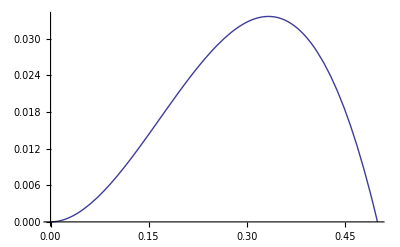

```mathematica
P[e_]:=(tmpdΓdk[[2]]/Γ/.k[4,0]->e)
tmp=P[Ratio[e/m] m]//Simplify
tmp/.subΓ0/.Ratio[_]->r/.subΓ/.Mev->1
Plot[%,{r,0,.5}]
```

(I)

```mathematica
"Given the interaction term:"
DefPrint["e1157",Subscript[L, 1]->g A1 B1 C1]
"The topology of the second-order interaction terms only allows 3 kinds of non-zero diagrams: AA->AA, AA->BB, and AB->AB"

GraphPlot[{{1->6,"A"},{6->7,"C"},{2->7,"B"},{6->3,"B"},{7->4,"B"}},VertexCoordinateRules->{1->{0,.5},2->{0,-.5},3->{1,.5},4->{1,-.5}}
]
```

Given the interaction term:

e1157: L_1→A1 B1 C1 g

```mathematica
"The topology of the second-order interaction terms only allows 3 kinds of order g^2 diagrams:  AA->BB, and AB->AB"
```

```mathematica
"The topology of the second-order interaction terms only allows 3 kinds of order \!\(\*SuperscriptBox[\(g\), \(2\)]\) diagrams:  AA->BB, AB->AC, and AB->AB.
This leads to the following terms:"

T==(⟨BB|AA⟩+⟨AB|AB⟩)

⟨BB|AA⟩==g^2(1/(Subscript[m, C]^2+(Subscript[k, A1]-Subscript[k, B1])^2)+1/(Subscript[m, C]^2+(Subscript[k, A1]-Subscript[k, B2])^2))
⟨BB|AA⟩->g^2(1/(Subscript[m, C]^2+t)+1/(Subscript[m, C]^2+u))

⟨AB|AB⟩==g^2(1/(Subscript[m, C]^2+(Subscript[k, A1]+Subscript[k, B1])^2)+1/(Subscript[m, C]^2+(Subscript[k, A1]-Subscript[k, B2])^2))
⟨AB|AB⟩->g^2(1/(Subscript[m, C]^2+s)+1/(Subscript[m, C]^2+u))
"where the s,t,u channel energies are indicated."
```

The topology of the second-order interaction terms only allows 3 kinds of order g^2 diagrams:  AA->BB, AB->AC, and AB->AB.
This leads to the following terms:

T==⟨BB|AA⟩+⟨AB|AB⟩

⟨BB|AA⟩==g^2 (1/((k_A1-k_B2)^2+m_C^2)+1/(m_C^2+(k_A1-k_B1)^2))

⟨BB|AA⟩→g^2 (1/(u+m_C^2)+1/(m_C^2+t))

⟨AB|AB⟩==g^2 (1/((k_A1-k_B2)^2+m_C^2)+1/(m_C^2+(k_A1+k_B1)^2))

⟨AB|AB⟩→g^2 (1/(u+m_C^2)+1/(m_C^2+s))

where the s,t,u channel energies are indicated.